```mathematica
(* 1 au =931.5 MeV  *) 
mbe8=7473.01-18.15;
mbe8s=mbe8+18.15;
mhe4=3727.38;
BeHe4=20.21;
dm=BeHe4;
mhe4s=mhe4+BeHe4;
m=mhe4s;
m3=mhe4;
me=0.51099907;
me=me*1;
m1=me;
q2min=(2me)^2;
q2max=(m-m3)^2;
qmin=2 me;
qmax=m-m3;


e3[q_]:=(m^2+m3^2-q^2)/(2m);
p3[q_]:=Sqrt[(m^2-(m3+q)^2)(m^2-(m3-q)^2)]/(2*m);
eq[q_]:=(m^2-m3^2+q^2)/(2m);
pq[q_]:=p3[q];

p1s[q_]:=Sqrt[q^2/4-me^2];
p2s[q_]:=Sqrt[q^2/4-me^2];
e1s[q_]:=q/2.;
e2s[q_]:=q/2.;
gamma[q_]=eq[q]/q;
vel[q_]:=(Sqrt[eq[q]^2-q^2]/eq[q]);

e1min[q_]:=eq[q]/2.-pq[q]/q*p1s[q]
e1max[q_]:=eq[q]/2.+pq[q]/q*p1s[q]

(*
e1[q_,cos_]  :=gamma[q]*(e1s[q]+vel[q]*p1s[q]*cos);
e2[q_,cos_]  :=gamma[q]*(e1s[q]-vel[q]*p1s[q]*cos);
*)
e1[q_,cos_]  :=eq[q]/2+pq[q]/q*p1s[q]*cos;
e2[q_,cos_]  :=eq[q]/2-pq[q]/q*p1s[q]*cos;
p1z[q_,cos_]:=pq[q]/2+eq[q]/q*p1s[q]cos;
p2z[q_,cos_]:=pq[q]/2-eq[q]/q*p1s[q]cos;
p1x[q_,cos_]:=p1s[q]Sqrt[1.-cos^2];
p2x[q_,cos_]:=-p1s[q]Sqrt[1.-cos^2];

p1[q_,cos_]  :=Sqrt[e1[q,cos]^2-me^2];
p2[q_,cos_]  :=Sqrt[e2[q,cos]^2-me^2];

e3min=e3[qmax];
e3max=e3[qmin];

p3q[q_]:=(m^2-m3^2-q^2)/2.;
p1q[q_]:=q^2/2.;
p1p2[q_]:=(q^2-2me^2)/2.;

ap3p1[q_,cos_]:=(m^2-m3^2-m*gamma[q]*q)/2-gamma[q]*vel[q]* m *p1s[q]*cos ;
ap3p2[q_,cos_]:=(m^2-m3^2-m*gamma[q]*q)/2+gamma[q]*vel[q]* m* p1s[q]*cos ;

p3p1[q_,cos_]:=e3[q]*e1[q,cos]+p3[q]*p1z[q,cos];
p3p2[q_,cos_]:=e3[q]*e2[q,cos]+p3[q]*p2z[q,cos];
mqcos[q_,cos_]:=2*p3p1[q,cos]*p3p2[q,cos]-m3^2*q^2/2. ;
mqcosi[q_]:=Integrate[mqcos[q,cc],{cc,-1,1}];
(*
me2[q_]:=(4 Pi)^2*[2*((m*gamma[q])^2*(e1s[q]^2-(vel[q]*p1s[q]*2/3))^2)-m3^2*(q^2-2 me^2)/2-me^2*m3^2);
*)
(*   Matrix element with zero electron mass    *)
mel0[q_,cc_]:=(1/8) (1-cc^2)(m^4+m3^4-2m3^2q^2+q^4-2m^2(m3^2+q^2));
mel0i[q_]:=Integrate[mel0[q,cc],{cc,-1,1}];

n2=(m^2-m3^2)^2*(1/6);

me2[q_]:=2*(2*( (m^2-m3^2-q^2)/4)^2-(m3*q)^2/2)-2*(2/3)*(m*pq[q]/(2*q))^2*(q^2-4*me^2);

me1[q_,cos_]:=(2*( (m^2-m3^2-q^2)/4)^2-(m3*q)^2/2)-2*cos^2*(m*pq[q]/(2*q))^2*(q^2-4*me^2);
mme1[q_]:=Integrate[me1[q,cc],{cc,-1,1}];


(* Formulas   *)
mxme2[q_,cos_]:=((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(8 q^2);  (* dm12 dOmega dOmega*   *)
mxme2i[q_]:=((2 me^2+q^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(6 q^2);                                      (* dm12 dOmega dphi*   *)
mxee2[q_,cos_]:=((q^2+cos^2 (4 me^2-q^2)) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)))/(2 4 m^2 q^2);        (* dE1 dE2   phase space    *)
mxee2i[q_]:=((m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q) (2 me^2+q^2))/(6  q^2); 
ms[q_]:=((dm^2-q^2) ((m+m3)^2-q^2) (2 me^2+q^2))/(6  q^2); (* the same as mxee2i but with dm *)
mse0[q_]:=((dm^2-q^2) ((m+m3)^2-q^2))/6;  (* me=0 *)
mse00[q_]:=(4 m^2(dm^2-q^2))/6; (*me=0 and dm<<m *)
mxmel02[q_,cos_]:=1/8 (1-cos^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2));                  (* me=0 dm12 dOmega dOmega*   *)
mxmel02i[q_]:=1/6 (m-m3-q) (m+m3-q) (m-m3+q) (m+m3+q);
mxmel002[q_,cos_]:=1/2 (1-cos^2) m^2 ((m-m3)^2-q^2);                  (* me=0 dm12 dOmega dOmega* \Delta M<<m  *)
mxmel002i[q_]:=2/3 m^2 ((m-m3)^2-q^2);

integralmxmel02i=4/45 (m-m3)^3 (m^2+3 m m3+m3^2);
                                              (* phase space dm12 dOm dOm* *)
mxphs[q_]:=(√(-me^2+q^2/4) √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(2 m)(4 π)(2π)/(2π)^5/(16 m^2); 
                                           (*me = 0 phase space dm12 dOm dOm* *)
mxphs0[q_]:=(q √((m^2-(m3-q)^2) (m^2-(m3+q)^2)))/(2 2 m)                    (4 π)(2π)/(2π)^5/(16 m^2);
mxphs00[q_]:=1/2 q √((m-m3)^2-q^2)                                        1/(64 m^2 π^3)      ;(* (4 π)(2π)/(2π)^5/(16 m^2)=1/(64 m^2 π^3)*)
                                             (* dG/dm *)
mxl0dGdm[q_,cos_]:=mxmel02[q,cos]*mxphs0[q];
mxl0dGdmi[q_]           :=mxmel02i[q]*mxphs0[q];

mxl00dGdm[q_,cos_]:=mxmel002i[q,cos]*mxphs00[q];
mxl00dGdmi[q_]           :=1/3 m^2 q ((m-m3)^2-q^2)^(3/2)    1/(64 m^2 π^3) ; (* (4 π)(2π)/(2π)^5/(16 m^2) =1/(64 m^2 π^3) *);

mxmedGdm[q_,cos_]:=mxme2[q,cos]*mxphs[q];
mxmedGdmi[q_]:=mxme2i[q]*mxphs[q];


(*   **********************************  *)



phs[q_]:= p3[q]*p1s[q]*(4 π)(2π)/(2π)^5/(16 m^2);
(*
p3[q_]:=Sqrt[(m^2-(m3+q)^2)(m^2-(m3-q)^2)]/(2*m);
p1s[q_]:=Sqrt[q^2/4-me^2];
*)
phs0[q_]:=q/2 Sqrt[dm^2-q^2] *(4 π)(2π)/(2π)^5/(16 m^2);
normphsp=1./(2*Pi)^5/(16*m^2)*4*Pi*2*Pi;
normme2=(4*Pi)^2;
normone=8*Pi/(m^5*5.97*10^(-13));
norm=normphsp*normme2*normone;

dgdq[q_]    :=me2[q]*phs[q];
dg00[q_]    :=mse00[q]*phs0[q];
dgdq2[q2_]:=me2[Sqrt[q2]]*phs[Sqrt[q2]]/(2*Sqrt[q2]);

dgdqa[q_,cos_]:=mqcos[q,cos]*phs[q];
    
                               
            (*  *****    Phace Space E1E3 *****   *)
inte1[x3_]:=Module[{q},q=Sqrt[(m-x3)*2*m-(m^2-m3^2)];NIntegrate[x1,{x1,e1min[q],e1max[q]}]];
 
normE1E3=(1/(2*Pi)^3)*(1/(8*m));
IntE1E3=NIntegrate[1,{x3,e3min,e3max},{x1,e1min[Sqrt[2m(m-x3)-(m^2-m3^2)]],e1max[Sqrt[2m(m-x3)-(m^2-m3^2)]]}];
             (*  *****    Phace Space M12 *****   *)
normM12=(1/(2*Pi)^5)*(1/(16*m^2))*4Pi*4Pi;
IntM12=NIntegrate[phs[q],{q,qmin,qmax}];


Print["E3max-E3min       = ",e3max-e3min]
Print["normE1E3          = ",normE1E3]
Print["IntE1E3           = ",IntE1E3]
Print["Phace Space(E1*E3)=",IntE1E3*normE1E3]
Print["normM12           = ",normM12]
Print["IntM12            =",IntM12]
Print["Phace Space(M12)  =",IntM12*normM12]
Print["Ratio(M12/ME1E3)  =",IntM12*normM12/(IntE1E3*normE1E3)]
Print["Ratio(ME1E3/M12)  =",IntE1E3*normE1E3/(IntM12*normM12)]
```

E3max-E3min       = 0.0543549

normE1E3          = 1.34468×10^-7

IntE1E3           = 0.72137

Phace Space(E1*E3)=9.70011×10^-8

normM12           = 7.17623×10^-11

IntM12            =4.85006×10^-8

Phace Space(M12)  =3.48051×10^-18

Ratio(M12/ME1E3)  =3.58811×10^-11

Ratio(ME1E3/M12)  =2.78698×10^10

```mathematica
(* Comparison of the total Width from archive and ne  *)
vpk=NIntegrate[mxl0dGdmi[q],{q,qmin,qmax}] ;
Chris=m^5/(4 Pi)^2/(8 Pi) *6.03 10^-13;
Print[" Chris Γ= (16 SuperscriptBox[G, 2] SuperscriptBox[π, 2] SuperscriptBox[α, 2])/Λ^4",Chris]
Print["vpk    Γ= (16 SuperscriptBox[G, 2] SuperscriptBox[π, 2] SuperscriptBox[α, 2])/Λ^4",vpk]
```

Chris Γ= (16 SuperscriptBox[G, 2] SuperscriptBox[π, 2] SuperscriptBox[α, 2])/Λ^4112.31

vpk    Γ= (16 SuperscriptBox[G, 2] SuperscriptBox[π, 2] SuperscriptBox[α, 2])/Λ^4111.638

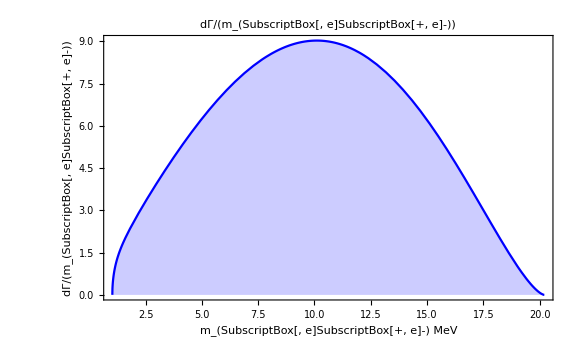

111.286

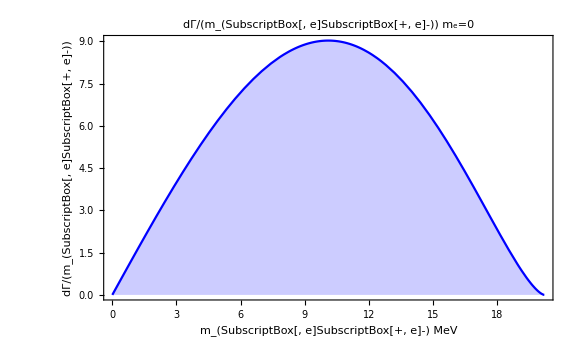

111.638

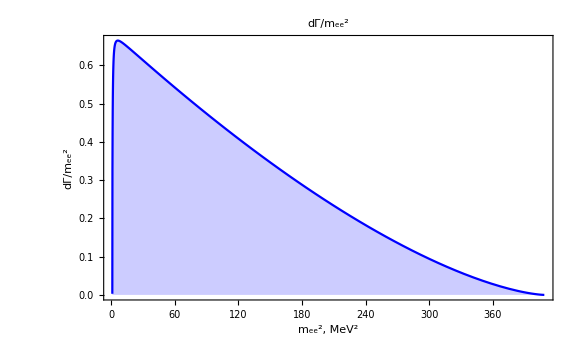

111.286

NormPHSP=3.58811×10^-11

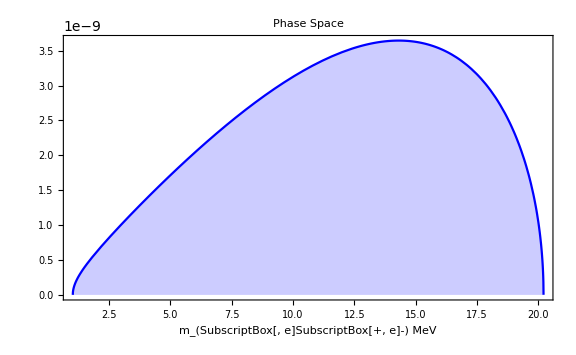

4.85006×10^-8

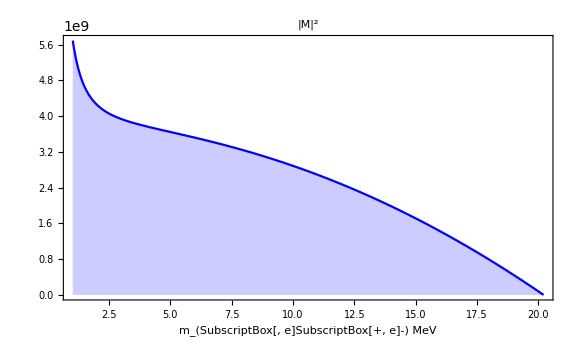

4.91158×10^10

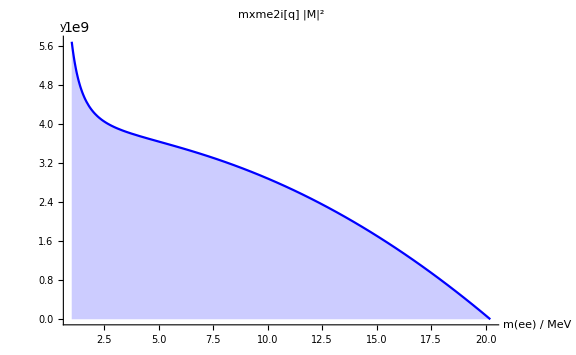

4.91158×10^10

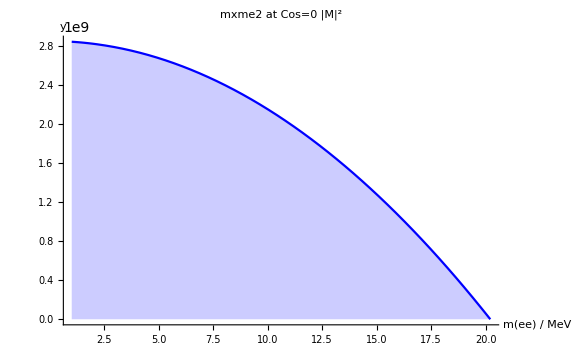

3.55228×10^10

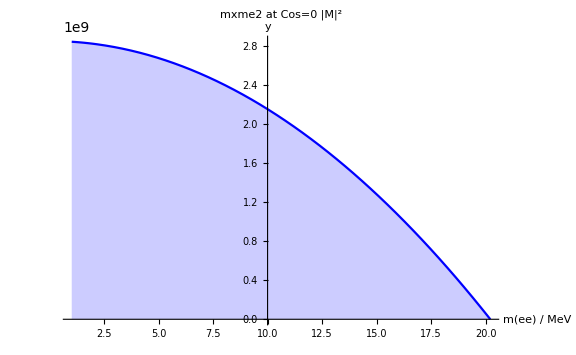

3.55228×10^10

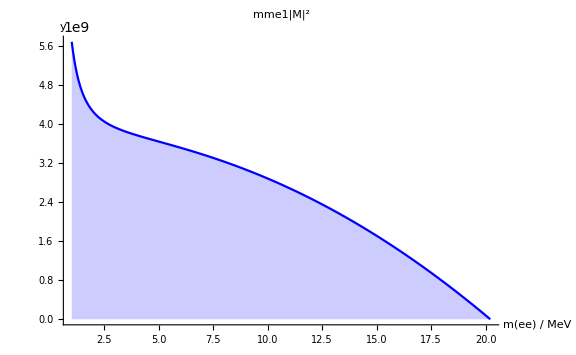

4.91158×10^10

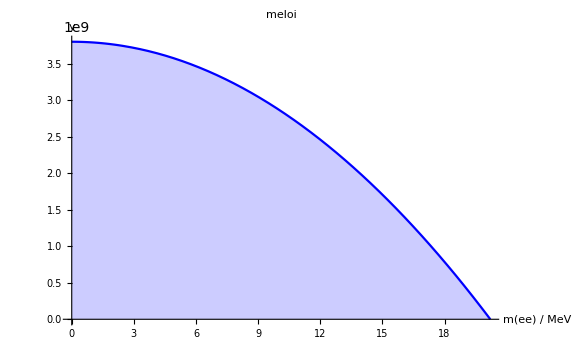

5.12477×10^10

-Graphics-

5.12477×10^10

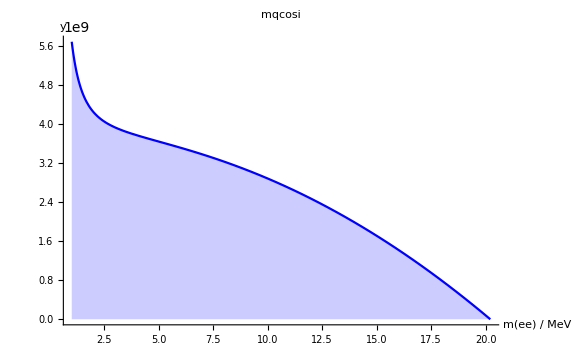

4.91158×10^10

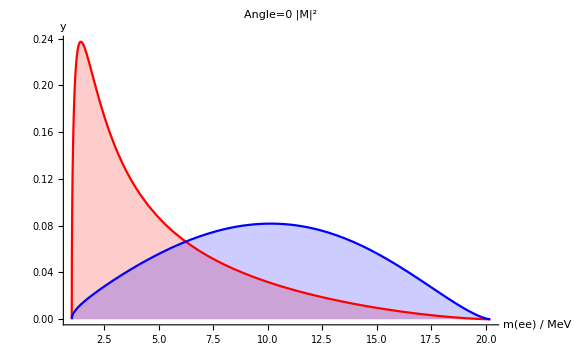

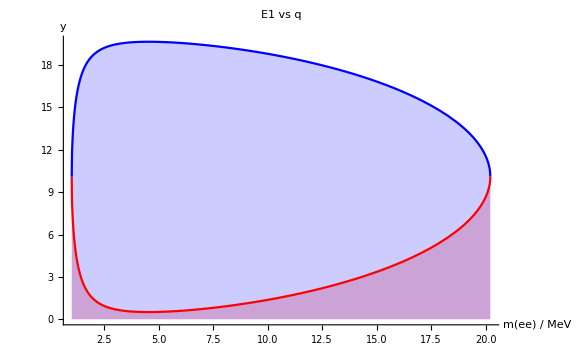

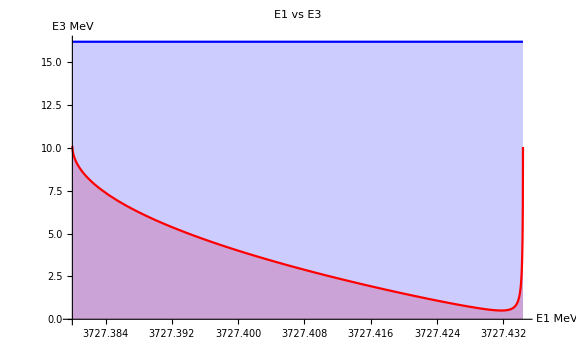

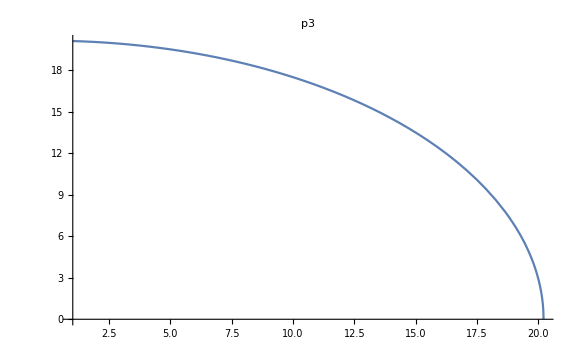

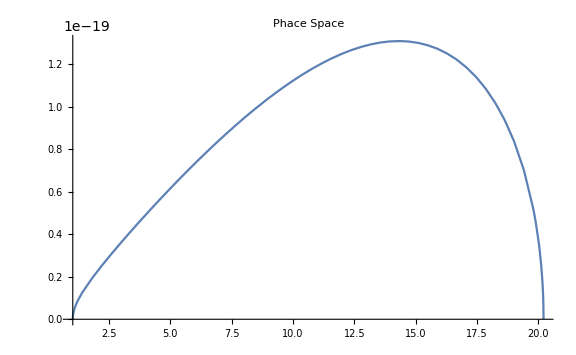

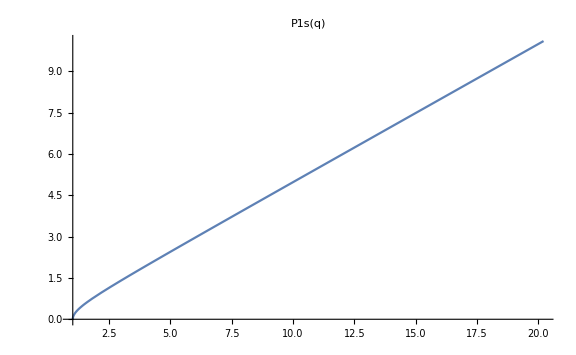

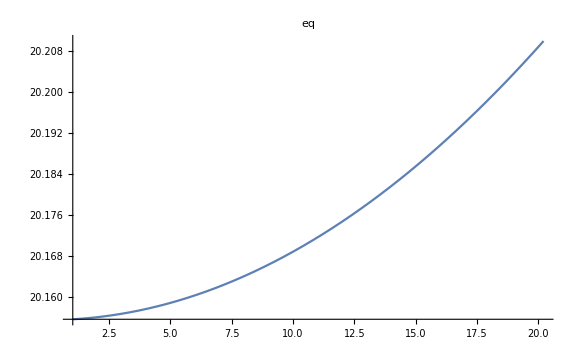

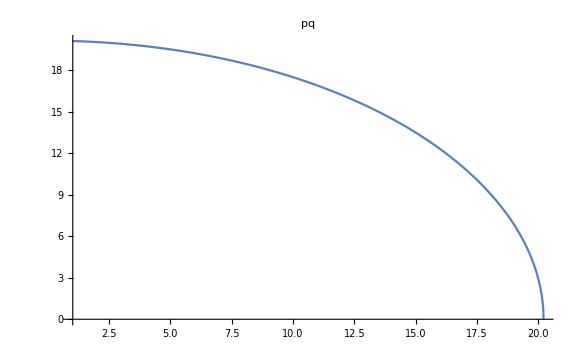

```mathematica
(*******************    P  L  O  T  S  *********************)
color1=Blue;
color2=Red;
(*       PLOT 1     *)
n2=NIntegrate[dgdq[qq],{qq,qmin,qmax}];
Plot[dgdq[q],                                {q,qmin,qmax},PlotLabel->"dΓ/(m_(SubscriptBox[, e]SubscriptBox[+, e]-))", PlotRange->{{0.,qmax},{0,All}},
Frame ->True, FrameLabel->{"m_(SubscriptBox[, e]SubscriptBox[+, e]-)   MeV","dΓ/(m_(SubscriptBox[, e]SubscriptBox[+, e]-))"},
Axes->True, AxesLabel->{"m_(SubscriptBox[, e]SubscriptBox[+, e]-)   MeV","dΓ/(m_(SubscriptBox[, e]SubscriptBox[+, e]-))"},
Filling->Axis,
PlotStyle->{color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
NIntegrate[dgdq[qq],{qq,qmin,qmax}]
n2=NIntegrate[mxl0dGdmi[qq],{qq,0.,qmax}];
(*       PLOT 2     *)
Plot[mxl0dGdmi[q],                     {q,0.,qmax},
PlotLabel->"dΓ/(m_(SubscriptBox[, e]SubscriptBox[+, e]-)) m_e=0",PlotRange->{{0,qmax},{0,All}},
Frame ->True, FrameLabel->{"m_(SubscriptBox[, e]SubscriptBox[+, e]-)   MeV","dΓ/(m_(SubscriptBox[, e]SubscriptBox[+, e]-))"},
Filling->Axis,
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
NIntegrate[mxl0dGdmi[qq],{qq,qmin,qmax}]
(*       PLOT 3     *)
Plot[dgdq2[q2],                     {q2,q2min,q2max},
PlotLabel->"dΓ/m_ee^2",
PlotRange->{{0,q2max},{0,All}},
Frame ->True, FrameLabel->{"m_ee^2, MeV^2","dΓ/m_ee^2"},
Filling->Axis,
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
NIntegrate[dgdq2[qq2],{qq2,q2min,q2max}]
(*     Plot 4     *)
normphs=NIntegrate[phs[qq],{qq,0.,qmax}];
Print["NormPHSP=",normphsp]
Plot[phs[q],                   {q,qmin,qmax},
PlotLabel->"Phase Space",
Frame ->True, FrameLabel->{"m_(SubscriptBox[, e]SubscriptBox[+, e]-)   MeV"," "},
PlotRange->{{0.,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
NIntegrate[phs[qq],{qq,qmin,qmax}]
(*     Plot 4    |M|^2  *)
n2=NIntegrate[me2[qq],{qq,qmin,qmax}];
Plot[me2[q],                   {q,qmin,qmax},
PlotLabel->"|M|^2",
Frame ->True, FrameLabel->{"m_(SubscriptBox[, e]SubscriptBox[+, e]-)   MeV"," "},
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
NIntegrate[me2[qq],{qq,qmin,qmax}]

n2=NIntegrate[mxme2i[qq],{qq,qmin,qmax}];
Plot[mxme2i[q],                   {q,qmin,qmax},
PlotLabel->"mxme2i[q] |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
n2

n2=NIntegrate[mxme2[qq,0.],{qq,qmin,qmax}];
Plot[mxme2[q,0.],                   {q,qmin,qmax},
PlotLabel->"mxme2 at Cos=0 |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
n2
n2=NIntegrate[mxme2[qq,0.],{qq,qmin,qmax}];
Plot[mxme2[q,0.],                   {q,qmin,qmax},
PlotLabel->"mxme2 at Cos=0 |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{10,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
n2


n2=NIntegrate[mme1[qq],{qq,qmin,qmax}];
Plot[mme1[q],                   {q,qmin,qmax},
PlotLabel->"mme1|M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
n2

n2=NIntegrate[mel0i[qq],{qq,0,qmax}];
Plot[{mel0i[q]},                   {q,0,qmax},
PlotLabel->"meloi",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
n2

n2=NIntegrate[mel0i[qq],{qq,0,qmax}];
Plot[{mxmel0i[q]},                   {q,0,qmax},
PlotLabel->"mxmeloi",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
n2

n2=NIntegrate[mqcosi[qq],{qq,qmin,qmax}];
Plot[mqcosi[q],                   {q,qmin,qmax},
PlotLabel->"mqcosi",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
NIntegrate[mqcosi[qq],{qq,qmin,qmax}]

norm1=NIntegrate[dgdqa[qq,1.],{qq,qmin,qmax}];
norm0=NIntegrate[dgdqa[qq,0.],{qq,qmin,qmax}];
norm05=NIntegrate[dgdqa[qq,0.5],{qq,qmin,qmax}];
Plot[{dgdqa[q,1.]/norm1, dgdqa[q,0.]/norm0},                  {q,qmin,qmax},
PlotLabel->"Angle=0 |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]

Plot[{e1min[q],e1max[q]},                   {q,qmin,qmax},
PlotLabel->"E1 vs q",
FrameLabel->{"mm(ee) MeV","E1"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2,color1},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
Plot[{e1min[Sqrt[2m(m-x3)-(m^2-m3^2)]],e1max[Sqrt[2m(m-3727.40)-(m^2-m3^2)]]},{x3,e3min,e3max},
PlotLabel->"E1 vs E3",
FrameLabel->{"E3 MeV","E1 MeV"},
PlotRange->{{e3min,e3max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"E1 MeV","E3 MeV"},
PlotStyle->{color2,color1}
]

Plot[p3[q],                        {q,qmin,qmax},PlotLabel->"p3"]
Plot[phs[q]*normphsp,{q,qmin,qmax},PlotLabel->"Phace Space"]
Plot[p1s[q],                      {q,qmin,qmax},PlotLabel->"P1s(q)"]

Plot[eq[q],                     {q,qmin,qmax},PlotLabel->"eq"]
Plot[pq[q],                     {q,qmin,qmax},PlotLabel->"pq"]

Plot[e3[q],                   {q,qmin,qmax},PlotLabel->"e3"]
Plot[e1min[q],             {q,qmin,qmax},PlotLabel->"e1_min"]
Plot[e1max[q],             {q,qmin,qmax},PlotLabel->"e1_max"]

Plot[gamma[q],             {q,qmin,qmax},PlotLabel->"gamma"]
Plot[vel[q],                  {q,qmin,qmax},PlotLabel->"velocity"]
Plot[p3q[q],                  {q,qmin,qmax},PlotLabel->"p3q"]
Plot[p3p1[q,1.],                {q,qmin,qmax},PlotLabel->"p3p1"]
Plot[p1q[q],                  {q,qmin,qmax},PlotLabel->"p1q"]

b=12/1000000;
min2=0;
max2=30^2;
Plot[Exp[-b*q2],                   {q2,min2,max2},
PlotLabel->"F(q2)",
FrameLabel->{"q2/GeV2","F(q2)"},
FrameLabel->{"m_(SubscriptBox[, e]SubscriptBox[+, e]-)   MeV","dΓ/(m_(SubscriptBox[, e]SubscriptBox[+, e]-))"},
PlotRange->{{min2,max2},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q2 / GeV2",y},
PlotStyle->{color2,color1}
]

Plot[inte1[x3],{x3,e3min,e3max},PlotLabel->"Int E1(E3)"]

Plot[Sqrt[2m(m-x3)-(m^2-m3^2)],{x3,e3min,e3max},
PlotLabel->"q vs E3",
FrameLabel->{"E3 MeV","q"},
PlotRange->{{e3min,e3max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"E3 / MeV",y},
PlotStyle->{color2}
]
Plot[phs[q],                   {q,qmin,qmax},
PlotLabel->"Phase Space",
FrameLabel->{"q/MeV","dPS/dq"},
PlotRange->{{0,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{color2}
]
```

```mathematica
(7.0627)^5 
(60 Pi)^0.2
7.0627 (60 Pi)^0.2
(60 Pi)^0.2 (60 Pi)^0.2 (60 Pi)^0.2 (60 Pi)^0.2 (60 Pi)^0.2 
Evaluate[60 Pi]
60*3.14152987
```

17573.3

2.85141

20.1387

188.496

60 π

188.492

```mathematica
me
```

0.510999

```mathematica
20.1^2-4me^2
```

402.966

```mathematica
20.1^2
```

404.01

```mathematica
4me^2
```

1.04448

```mathematica
dm
```

20.21

```mathematica
(20.137/dm)^5
```

0.98207